# Systematic Randomness Testing

Emmy/Noah Blumenthal

Jonathan Gorard

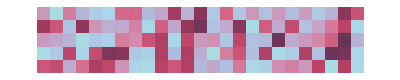

```mathematica
ArrayPlot[Partition[RandomReal[{0,1},125],25],]
```

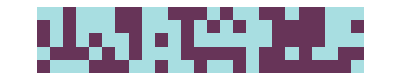

```mathematica
ArrayPlot[Partition[Take[rule30seq,125],25],]
```

## Introduction

[introduce why randomness testers are important]

In this investigation, we will explore both empirically–derived and theoretically–derived randomness tests.

We will explore both empirically–derived tests and theoretically derived tests.

```mathematica
Grid[{{"","Monte Carlo method","Theoretical method"},{"0s and 1s","OPERM5
Serial","Chi square
Spectral
Runs
CUSUM
Arcsine law
Kolmogorov–Smirnov"},{"Reals between 0 and 1","Runs (length)
Runs (counts)","Chi square
Spectral
Differences
Kolmogorov–Smirnov"}},Dividers->All]//Text
```

| Monte Carlo method | Theoretical method
0s and 1s | OPERM5
Serial | Chi square
Spectral
Runs
CUSUM
Arcsine law
Kolmogorov–Smirnov
Reals between 0 and 1 | Runs (length)
Runs (counts) | Chi square
Spectral
Differences
Kolmogorov–Smirnov

## Chi square equidistribution test

The first test we will examine is a relatively simple, ubiquitous test: the chi square test for independence. In this approach we will use the chi square test to measure how the observed values differ from expected values.

#### Zeros and ones

The expected value distribution of zeros and ones is very simple. There is a 1/2 probability that a variate will be 0 and a 1/2 probability that a variate will be 1. Therefore, we can set up a statistic like the following:

```mathematica
chiSquareTestStatIntegers[seq_]:=(Total[seq]-1/2 Length[seq])^2/(1/2 Length[seq])(*observed number of ones*)+((Length[seq]-Total[seq])-1/2 Length[seq])^2/(1/2 Length[seq])(*observed number of zeros*);
```

We know that this statistic will follow a chi square distribution with ν = 1. Let’s confirm:

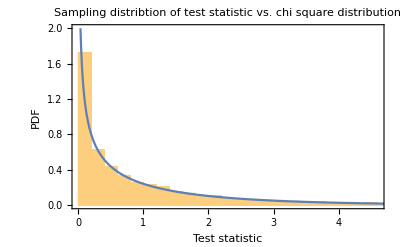

```mathematica
Show[Histogram[Table[chiSquareTestStatIntegers[RandomInteger[{0,1},10000]],100000],Automatic,"PDF"],Plot[PDF[ChiSquareDistribution[1],x],{x,0,10},PlotRange->{0,2}],]
```

Therefore, we can construct a p-value as follows:

```mathematica
chiSquareTestPValueIntegers[seq_]:=1.-CDF[ChiSquareDistribution[1],chiSquareTestStatIntegers[seq]]
```

To check our work, we can construct a probability plot comparing the distribution of p-values to the uniform distribution.

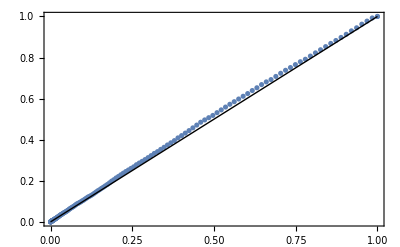

```mathematica
ProbabilityPlot[Table[chiSquareTestPValueIntegers[RandomInteger[{0,1},10000]],10000],UniformDistribution[]]
```

We observe that the rate of type-I error behaves as expected for a well-functioning test. This, of course, assumes that the pseudo–random number generator that is RandomInteger is truly “random”—whatever that may mean.

#### Random reals between zero and one

Again, with the chi square test for independence, we must compare observed values to expected values. For continuous distributions, we must choose bins in which we have expected values. For our purposes, we will choose bins of size 1/n where n is the length of the sequence. Using this bin specification, we know that the expected number of numbers we should observe in each bin should be 1. With this information, we can create a test statistic:

```mathematica
chiSquareTestStatReals[seq_]:=Total[(BinCounts[seq,1/Length[seq]]-1)^2/1](*note we use the listable atribute of squaring and basic arithmetic*)
```

This distribution should follow the chi square distribution with ν = n -2 where n is the length of the sequence. Let’s confirm:

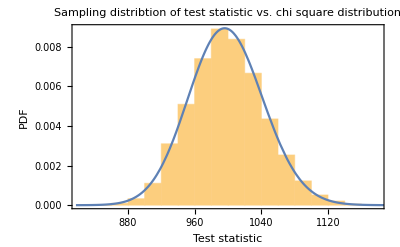

```mathematica
Show[Histogram[Table[chiSquareTestStatReals[RandomReal[{0,1},1000]],10000],Automatic,"PDF"],Plot[PDF[ChiSquareDistribution[998],x],{x,0,1500},],]
```

We can then construct a p-value:

```mathematica
chiSquareTestPValueReals[seq_]:=1.-CDF[ChiSquareDistribution[Length[seq]-2],chiSquareTestStatReals[seq]];
```

Again, to check our work, we can construct a probability plot comparing the distribution of p-values to the uniform distribution.

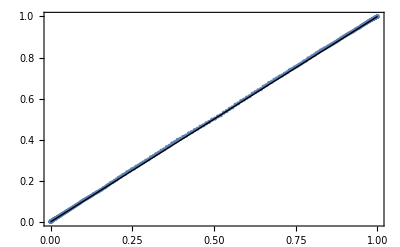

```mathematica
ProbabilityPlot[Table[chiSquareTestPValueReals[RandomReal[{0,1},1000]],10000],UniformDistribution[]]
```

Again, it seems as if we are successful!

## The Kolmogorov–Smirnov distribution fit test

The Kolmogorov–Smirnov test is a power distribution fit test that compares an empirical CDF to a known CDF. The Kolmogorov–Smirnov test is relatively simple to formulate, but fortunately, it is already implemented in the Wolfram Language. We can then apply it to test for equidistribution of a sequence:

```mathematica
sequence=RandomReal[{0,1},10000];
```

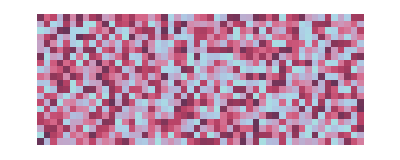

```mathematica
ArrayPlot[Partition[Take[sequence,1000],50],ImageSize->Full,ColorFunction->"CandyColors"]
```

```mathematica
KolmogorovSmirnovTest[sequence,UniformDistribution[]]
```

0.383461

It is important to note that the Kolmogorov–Smirnov test does not handle ties very well:

```mathematica
duplicateSequence=Flatten[{sequence,sequence}];
```

```mathematica
KolmogorovSmirnovTest[duplicateSequence,UniformDistribution[]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.0745876

#### A remark on equidistribution tests

Equidistribution tests are very easily fooled! They do not care about order, permutations, runs, spectra, or anything like these complex properties. Here’s an example of how equidistribution tests is completely fooled:

```mathematica
nonrandomSequence=Range[0,1,.0001];
```

```mathematica
KolmogorovSmirnovTest[nonrandomSequence,UniformDistribution[]]
```

1.

```mathematica
chiSquareTestPValueReals[nonrandomSequence]
```

General::munfl: Exp[-37587.9] is too small to represent as a normalized machine number; precision may be lost.

1.

## Serial test

The serial test examines the frequency of the following pairs within the overall sequence:

```mathematica
Row[Tuples[{0,1},2],"     "]
```

{0,0}{0,1}{1,0}{1,1}

For example, the sequence

```mathematica
sequence=RandomInteger[{0,1},100];
sequence//Row
```

1101011001101110111100101100100110011000110110000011101111100000110011001100000111100101000111101010

has the associated counts

```mathematica
SequenceCount[sequence,#]&/@Tuples[{0,1},2]
```

{16,23,24,21}

where the order is that of the pairs list above.

We can create a chi square–like statistic that measures the deviation from expected frequency

stat = (freq_(0,0)-n µ_(freq. 0,0))^2/(n µ_(freq. 0,0))+(freq_(0,1)-n µ_(freq. 0,1))^2/(n µ_(freq. 0,1))+(freq_(1,1)-n µ_(freq. 1,1))^2/(n µ_(freq. 1,1))+(freq_(1,0)-n µ_(freq. 1,0))^2/(n µ_(freq. 1,0))

where n is the sequence length and μ_freq is the expected frequency with which the the pair occurs. These frequencies are computed empirically:

```mathematica
mcts[n_,samplesize_]:=Mean[Table[N@SequenceCount[RandomInteger[{0,1},n],#]&/@Tuples[{0,1},2],samplesize]];
```

This function counts the mean number of pairs of a particular type observed within a large number, samplesize, of random sequences.

We can observe how these expected frequencies vary with sequence length:

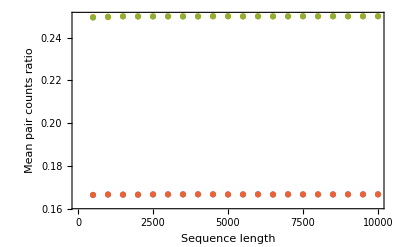

```mathematica
{pts00,pts01,pts10,pts11}=ParallelTable[{{n,n,n,n},mcts[n,10000]/n}ᵀ,{n,500,10000,500}]ᵀ;
ListPlot[{pts00,pts01,pts10,pts11},Frame->True,FrameLabel->{"Sequence length","Mean pair counts ratio"}]
```

This figure displays how the expected frequencies are invariant under sequence length variation.

After discovering this, we can come up with one set of constants that will work for any sequence length:

```mathematica
$mctsrat=mcts[1000,100000]/1000
```

{0.166564,0.249761,0.249774,0.166603}

And with this in mind we can finally construct a test statistic:

```mathematica
SerialTestStat[seq_]:=Total[((SequenceCount[seq,#]&/@Tuples[{0,1},2])-Length[seq]$mctsrat)^2/(Length[seq]$mctsrat)];
```

As we chose a chi square–like statistic, we can anticipate that the test statistic will follow a gamma distribution.

```mathematica
serialsamplingdist[n_,samplesize_]:=ParallelTable[SerialTestStat[RandomInteger[{0,1},n]],samplesize]
```

```mathematica
serialdistsample1000=serialsamplingdist[1000,100000];
```

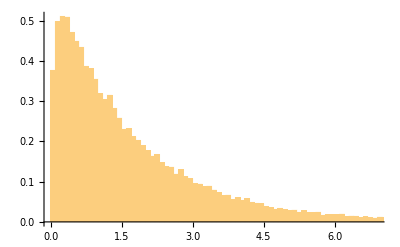

```mathematica
Histogram[serialdistsample1000,{.1},"PDF"]
```

```mathematica
serialfitdist1000=FindDistribution[serialdistsample1000,TargetFunctions->{GammaDistribution}]
```

GammaDistribution[1.12212,1.53172]

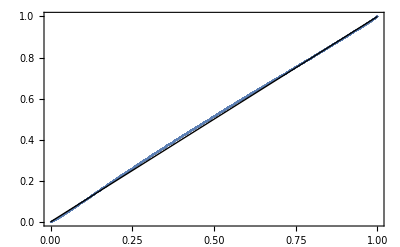

```mathematica
ProbabilityPlot[serialdistsample1000,serialfitdist1000]
```

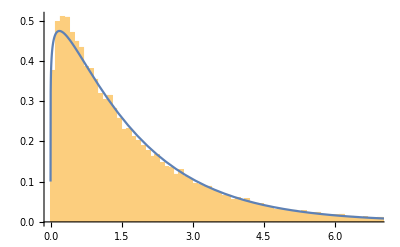

```mathematica
Show[Histogram[serialdistsample1000,{.1},"PDF"],Plot[PDF[serialfitdist1000,x],{x,0,10}]]
```

We can see that this distribution fits relatively well. Let’s now investigate how the distribution parameters α and β vary with sequence length.

```mathematica
αβparams[n_,samplesize_]:=FindDistributionParameters[serialsamplingdist[n,samplesize],GammaDistribution[α,β]]
```

```mathematica
paramvslength=Table[{{n,n},{α,β}}ᵀ/.αβparams[n,10000],{n,100,10000,1000}];
```

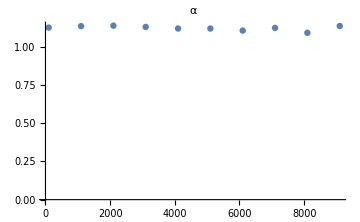
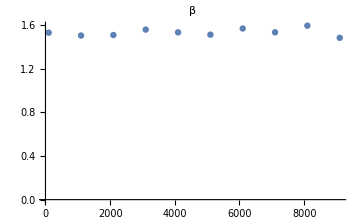

```mathematica
Row@{ListPlot[paramvslengthᵀ⟦1⟧,],ListPlot[paramvslengthᵀ⟦2⟧,]}
```

We can see that the parameters hardly vary and do not vary consistently with list length. We can then find parameters we like.

```mathematica
$serialparams=αβparams[10000,10000]
```

{α→1.10793,β→1.53947}

```mathematica
$serialfitdist=GammaDistribution[α,β]/.$serialparams
```

GammaDistribution[1.10793,1.53947]

Our p–value is then of the form:

```mathematica
1-CDF[$serialfitdist,SerialTestStat[RandomInteger[{0,1},10000]]]
```

0.522471

As a final test, we want to confirm that the distribution of p–values follows a uniform distribution:

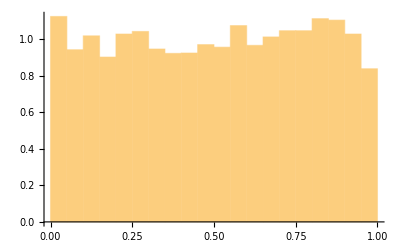

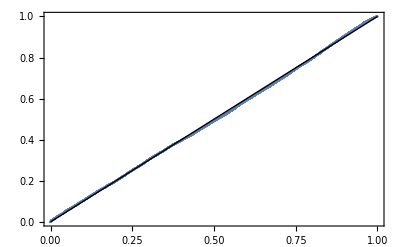

```mathematica
1-CDF[$serialfitdist,SerialTestStat[#]]&/@RandomInteger[{0,1},{10000,10000}];
Histogram[%,Automatic,"PDF"]
ProbabilityPlot[%%,UniformDistribution[]]
```

We can see that the p–values are uniformly distributed from our Monte Carlo method.

#### Discussion

This method is powerful as it examines the frequency and ordering of pairs. However, this method is contingent on one large assumption—that the Wolfram Language pseudorandom number generator is truly pseudorandom. Or rather, that it is pseudorandom enough. A Monte Carlo approach is often very powerful for these sorts of statistics; however, it is important to be weary of such assumptions.

## Runs tests

In these tests, we will investigate runs of both 0s and 1s and random reals between 0 and 1. A run is a sequence that fits a particular pattern until it is reset. For random reals, we will use increasing runs. For example, in the sequence

```mathematica
sequence=RandomReal[{0,1},100];
Row[sequence,", "]
```

, , 0.1962730.5101910.2431160.2738660.4225780.4678930.3280390.1124530.5452070.9751390.131560.1640650.8165840.2001550.1359940.02825740.9182440.8422110.8247470.2888780.1682090.9681040.4529360.7635120.1827590.5069150.5700640.5525840.4088060.9509030.714370.2599670.6489820.1148130.1368540.4225090.6259280.8544650.5518830.4894410.7306840.0618610.686620.4571820.7924270.01560280.8835250.4396950.7728690.2102590.5590940.2939650.4819530.9016610.02184970.1321740.1954480.09894230.9257040.7198420.2960460.1103210.7751270.4282470.9658330.06196820.3832110.09147820.07268630.3031080.6373970.8102780.5463480.5168330.2674020.6510380.143990.5814620.04380790.7573170.1898980.5000740.5600880.9344750.6371360.0439320.4990310.799790.4095870.3278040.5951680.4520280.2275550.7754630.5403420.3757730.5767670.3834230.9622330.0575503

The associated runs are

```mathematica
Row[Split[sequence,#1<#2&],", "]
```

, , {0.196273,0.510191}{0.243116,0.273866,0.422578,0.467893}{0.328039}{0.112453,0.545207,0.975139}{0.13156,0.164065,0.816584}{0.200155}{0.135994}{0.0282574,0.918244}{0.842211}{0.824747}{0.288878}{0.168209,0.968104}{0.452936,0.763512}{0.182759,0.506915,0.570064}{0.552584}{0.408806,0.950903}{0.71437}{0.259967,0.648982}{0.114813,0.136854,0.422509,0.625928,0.854465}{0.551883}{0.489441,0.730684}{0.061861,0.68662}{0.457182,0.792427}{0.0156028,0.883525}{0.439695,0.772869}{0.210259,0.559094}{0.293965,0.481953,0.901661}{0.0218497,0.132174,0.195448}{0.0989423,0.925704}{0.719842}{0.296046}{0.110321,0.775127}{0.428247,0.965833}{0.0619682,0.383211}{0.0914782}{0.0726863,0.303108,0.637397,0.810278}{0.546348}{0.516833}{0.267402,0.651038}{0.14399,0.581462}{0.0438079,0.757317}{0.189898,0.500074,0.560088,0.934475}{0.637136}{0.043932,0.499031,0.79979}{0.409587}{0.327804,0.595168}{0.452028}{0.227555,0.775463}{0.540342}{0.375773,0.576767}{0.383423,0.962233}{0.0575503}

For another sequence of 0s and 1s, we obtain the runs by simply splitting the list:

```mathematica
sequence=RandomInteger[{0,1},100];
Row[sequence]
```

1000010111111100010100100100100100000001101110101100111101100001000111100010100110101001100011100000

```mathematica
Row[Split[sequence],", "]
```

, , {1}{0,0,0,0}{1}{0}{1,1,1,1,1,1,1}{0,0,0}{1}{0}{1}{0,0}{1}{0,0}{1}{0,0}{1}{0,0}{1}{0,0,0,0,0,0,0}{1,1}{0}{1,1,1}{0}{1}{0}{1,1}{0,0}{1,1,1,1}{0}{1,1}{0,0,0,0}{1}{0,0,0}{1,1,1,1}{0,0,0}{1}{0}{1}{0,0}{1,1}{0}{1}{0}{1}{0,0}{1,1}{0,0,0}{1,1,1}{0,0,0,0,0}

Now that we have a definition of runs, we can begin creating statistics using them.

### How long are runs in a sequence?

The first statistic we will construct will measure the length of runs. Our approach will again utilize a Monte Carlo method. To measure runs:

```mathematica
runsup[seq_]:=Split[seq,#1<#2&];
```

In order to count lengths of runs:

```mathematica
runLengthDist[seq_]:=Length/@runsup[seq]
```

The distribution of run lengths within a random sequence:

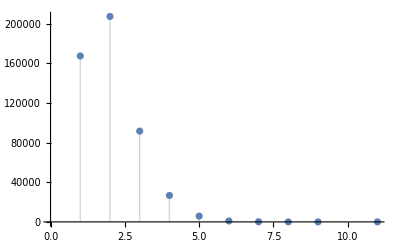

```mathematica
ListPlot[Counts@runLengthDist@RandomReal[{0,1},1000000],Filling->Axis]
```

We then want to investigate if these ratios vary with sequence length:

```mathematica
sequence=RandomReal[{0,1},10000];
Manipulate[Histogram[runLengthDist[Take[sequence,n]],{1},"PDF",PlotRange->{{0,10},{0,1}},PlotLabel->"n = "<>ToString[n]],{n,1,10000,1}]
```

We can see that the run lengths quickly converge to a constant distribution. With this we can then calculate a constant–the mean run length:

```mathematica
$meanRunLength=Mean[ParallelMap[ N@Mean[runlengthDist[#]]&,RandomReal[{0,1},{10000,5000}]]]
```

1.99988

We will then construct another chi–square like test statistic:

```mathematica
RunLengthStat[seq_]:=Total[(runLengthDist[seq]-$meanRunLength)^2/($meanRunLength)];
```

We then need to assess the distribution of this test statistic:

```mathematica
Manipulate[Histogram[RunLengthStat/@RandomReal[{0,1},{1000,seqleng}]],{seqleng,5000}]
```

We can see that this distribution fits the normal distribution relatively well:

```mathematica
Manipulate[ProbabilityPlot[RunLengthStat/@RandomReal[{0,1},{1000,seqleng}]],{seqleng,5000}]
```

Next, we will demonstrate that the mean follows a linear trend and is proportional to the sequence length

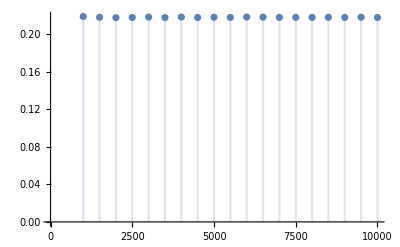

```mathematica
DiscretePlot[Mean[RunLengthStat[#]&/@RandomReal[{0,1},{1000,seqleng}]]/seqleng,{seqleng,1000,10000,500}]
```

We can then construct a function that will return the approximate sample mean:

```mathematica
runlengthμ[seqleng_]=seqleng Mean[RunLengthStat[#]&/@RandomReal[{0,1},{10000,10000}]]/10000
```

0.218386 seqleng

We then proceed with a similar procedure regarding standard deviation—the other parameter for our distribution:

```mathematica
DiscretePlot[StandardDeviation[RunLengthStat[#]&/@RandomReal[{0,1},{10000,seqleng}]]/seqleng,{seqleng,1000,10000,500}]
```

$Aborted

We see that this is not quite a linear pattern. We can hypothesize using a non–linear model:

```mathematica
standarddevratvsseqleng=ParallelTable[{seqleng,StandardDeviation[RunLengthStat[#]&/@RandomReal[{0,1},{1000,seqleng}]]/seqleng},{seqleng,1000,10000,500}];
```

```mathematica
nlm=NonlinearModelFit[standarddevratvsseqleng,a x^b,{a,b},x]
```

FittedModel[0.47521/x^0.500196]

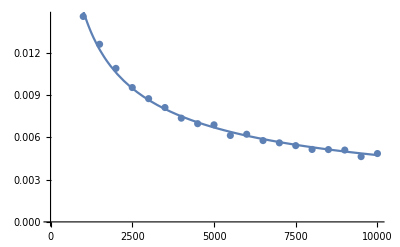

```mathematica
Show[ListPlot[standarddevratvsseqleng],Plot[nlm[seqleng],{seqleng,0,10000}]]
```

We see that this fits very well. We then have

σ/seqleng≈nlm[seqleng]
σ≈sqeleng nlm[seqleng]

```mathematica
runlengthσ[seqleng_]=seqleng nlm[seqleng]
```

0.47521 seqleng^0.499804

All together:

stat \[Distributed] NormalDistribution[statdistμ[seqleng],statdistσ[seqleng]]

Finally, we can calculate a two–tailed p–value given a sequence:

```mathematica
2Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[runlengthμ[Length[sequence]],runlengthσ[Length[sequence]]],RunLengthStat[sequence]]
```

0.601173

Like before, we will evaluate the rate of type I error by comparing the distribution of p–values to the uniform distribution:

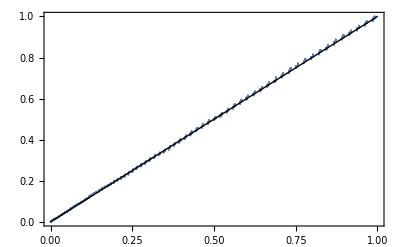

```mathematica
ProbabilityPlot[Table[2Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[runlengthμ[5000],runlengthσ[5000]],RunLengthStat[RandomReal[{0,1},5000]]],10000],UniformDistribution[]]
```

### How many runs do we expect a sequence to have?

The next statistic we create will count the total amount of runs a sequence has. The statistic is then:

```mathematica
RunCountStat=Length[Split[#,(#1<#2&)]]&;
```

This distribution follows a normal distribution:

```mathematica
Manipulate[Histogram[RunCountStat/@RandomReal[{0,1},{1000,seqleng}]],{seqleng,5000}]
```

```mathematica
Manipulate[ProbabilityPlot[RunCountStat/@RandomReal[{0,1},{1000,seqleng}]],{seqleng,5000}]
```

Again, we will investigate how the mean varies over sequence length:

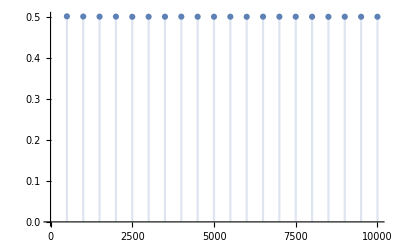

```mathematica
DiscretePlot[Mean[RunCountStat/@RandomReal[{0,1},{1000,seqleng}]]/seqleng,{seqleng,500,10000,500}]
```

The mean to sequence length ratio is constant, making the mean given a sequence length. This is unsurprising because as we observed before, the mean sequence length is two. Therefore, the mean number of runs should be half the sequence length.

```mathematica
runcountμ[seqleng_]=seqleng/2
```

seqleng/2

Standard deviation is a bit more complicated:

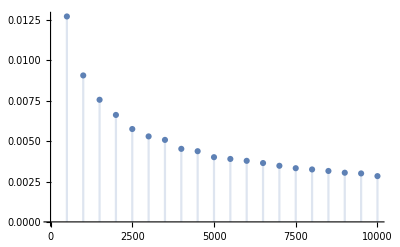

```mathematica
DiscretePlot[StandardDeviation[RunCountStat/@RandomReal[{0,1},{1000,seqleng}]]/seqleng,{seqleng,500,10000,500}]
```

Again, we get a non–linear pattern. Let’s fit a non–linear mode:

```mathematica
nlm=NonlinearModelFit[ParallelTable[{seqleng,StandardDeviation[RunCountStat/@RandomReal[{0,1},{1000,seqleng}]]/seqleng},{seqleng,500,10000,500}],a x^b,{a,b},x]
```

FittedModel[0.303833/x^0.506215]

The standard deviation given a sequence length is then:

```mathematica
runcountσ[seqleng_]=nlm[seqleng] seqleng
```

0.303833 seqleng^0.493785

We then have our distribution:

```mathematica
$runcountdist[seqleng_]=NormalDistribution[runcountμ[seqleng],runcountσ[seqleng]]
```

NormalDistribution[seqleng/2,0.303833 seqleng^0.493785]

We can finally compose a two–tailed p–value:

```mathematica
2Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[runcountμ[Length[sequence]],runcountσ[Length[sequence]]],RunCountStat[sequence]]
```

0.530441

And we will assess the rate of type I error:

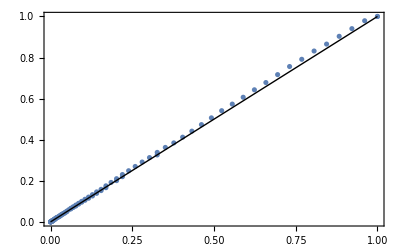

```mathematica
ProbabilityPlot[Table[2Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[runcountμ[5000],runcountσ[5000]],RunCountStat[RandomReal[{0,1},5000]]],10000],UniformDistribution[]]
```

### How many runs does a sequence of zeros and ones have?

This test is taken entirely from the NIST publication. It only assesses sequences of 0s and 1s. Additionally, it is theoretically derived. The test statistic the publication gives is

```mathematica
NISTRunsstat=Length@Split@#&;
```

And the publication assigns the associated p–value.

```mathematica
NISTRunspval=Erfc[Abs[Length@Split@#1-2 Length[#1] #2 (1-#2)]/(2. √(2Length[#1]) #2 (1-#2))]&[#,Total[#]/Length[#]]&;
```

We can demonstrate this test on a sequence:

```mathematica
sequence=RandomInteger[{0,1},10000];
NISTRunspval[sequence]
```

0.357017

Finally, we can assess this test by assessing the rate of type I error:

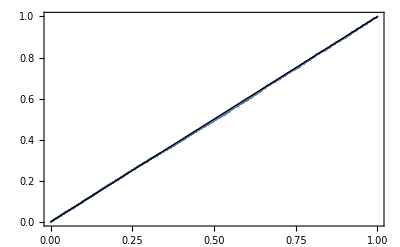

```mathematica
ProbabilityPlot[NISTRunspval/@RandomInteger[{0,1},{10000,10000}],UniformDistribution[]]
```

## Differences tests

## Overlapping permutations

## Spectral tests

## Sequential sums tests

## Arcsine test

## Variates of arbitrary distributions